```mathematica
1->123,2->1,3->"STOP"
```

```mathematica
init = {2,1,1};
tt2[x_]:=Piecewise[{{{2,1,3}, First[x]==1}, {{1}, First[x]==2}, {{0}, First[x]==3}}]
t2[x_]:=Piecewise[{{Delete[Delete[Flatten[Append[x,tt2[x]]],1],1], First[x]≠0}, {{0}, First[x]==0}}]
```

```mathematica
t2[init]
```

{1,1}

```mathematica
t2[%]
```

{2,1,3}

```mathematica
t2[%]
```

{3,1}

```mathematica
t2[%]
```

{0}

```mathematica
t2[%]
```

{0}

{{1,1},{2,1,3},{3,1},{0},{0}}

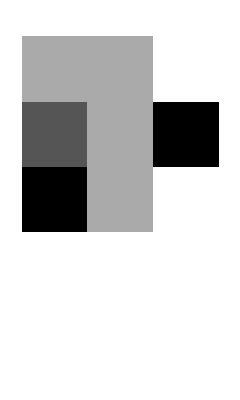

```mathematica
Table[Nest[t2,init,i],{i,1,5}]
ArrayPlot[%]
```

```mathematica
init = {2,1,2,2,2,2};
A={1,2,1,1};
B={1,0,2,1};
tt2[x_,a_,b_]:=Piecewise[{{{0}, First[x]==0}, {a, First[x]==1}, {b, First[x]==2}}]
t2[x_]:=Piecewise[{{Delete[Flatten[Append[x,tt2[x,A,B]]],1], First[x]≠0}, {{0}, First[x]==0}}]
```

{{1,2,2,2,2,1,0,2,1},{2,2,2,2,1,0,2,1,1,2,1,1},{2,2,2,1,0,2,1,1,2,1,1,1,0,2,1},{2,2,1,0,2,1,1,2,1,1,1,0,2,1,1,0,2,1},{2,1,0,2,1,1,2,1,1,1,0,2,1,1,0,2,1,1,0,2,1},{1,0,2,1,1,2,1,1,1,0,2,1,1,0,2,1,1,0,2,1,1,0,2,1},{0,2,1,1,2,1,1,1,0,2,1,1,0,2,1,1,0,2,1,1,0,2,1,1,2,1,1},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0}}

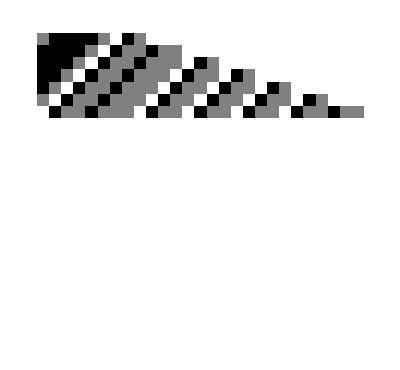

```mathematica
Table[Nest[t2,init,i],{i,1,25}]
ArrayPlot[%]
```

```mathematica
init = {1,1,1};
A={1,0};
tt1[x_,a_]:=Piecewise[{{{0}, First[x]==0}, {{a}, First[x]==1}}]
t1[x_]:=Piecewise[{{Delete[Flatten[Append[x,tt1[x,A]]],1], First[x]≠0}, {{0}, First[x]==0}}]
```

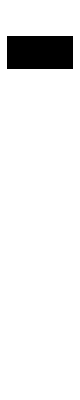
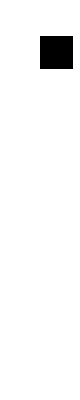
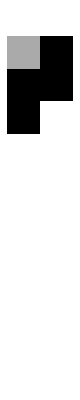
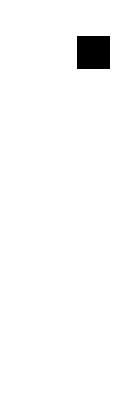
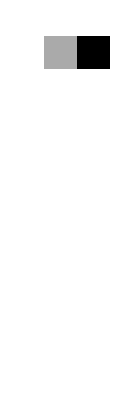
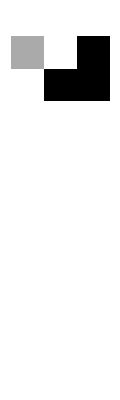
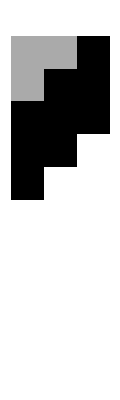
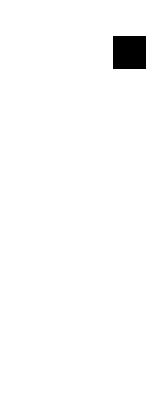

```mathematica
aa=aa+1;
A=IntegerDigits[aa];
Table[ArrayPlot[Table[Nest[t1,IntegerDigits[j,2],i],{i,1,10}]],{j,1,20}]
```

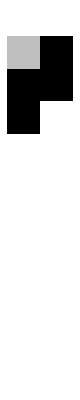
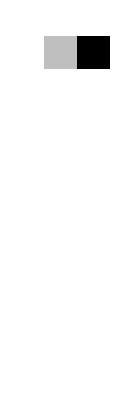
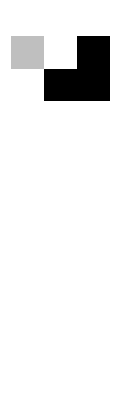
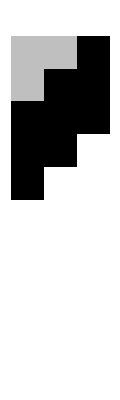
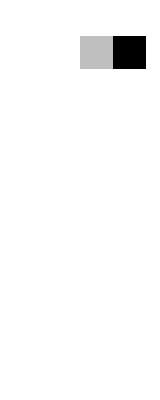
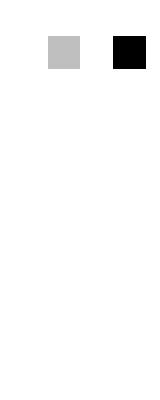
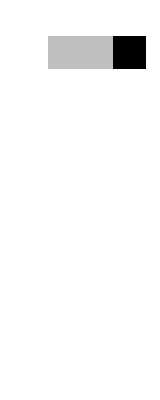
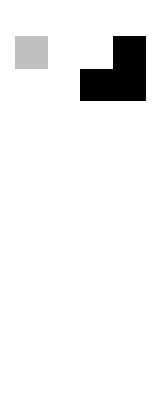
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
aa=aa+1;
A=IntegerDigits[aa];
Table[ArrayPlot[Table[Nest[t1,IntegerDigits[j,2],i],{i,1,10}]],{j,1,20}]
```

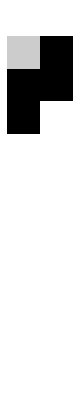
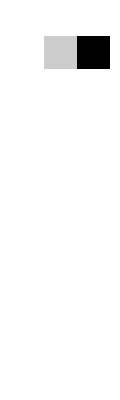
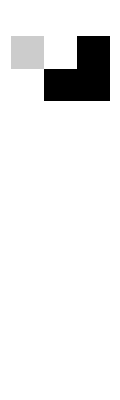
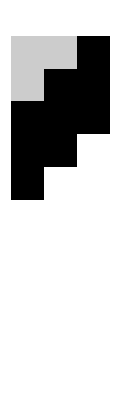
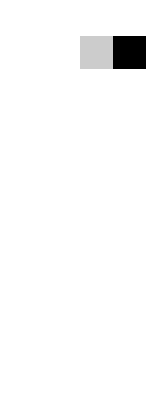
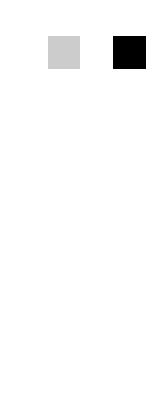
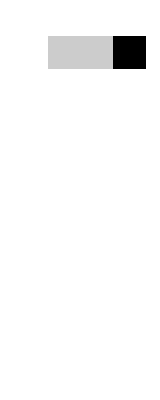
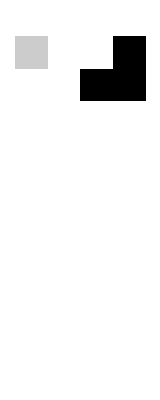
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
aa=aa+1;
A=IntegerDigits[aa];
Table[ArrayPlot[Table[Nest[t1,IntegerDigits[j,2],i],{i,1,10}]],{j,1,20}]
```

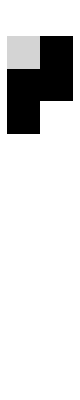
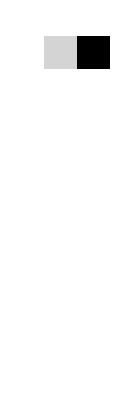
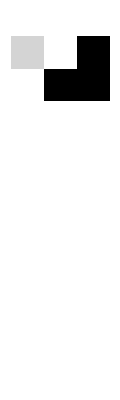
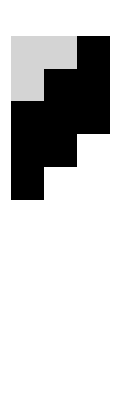
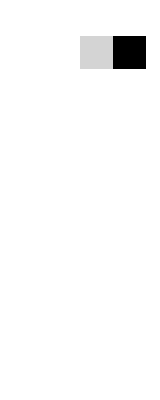
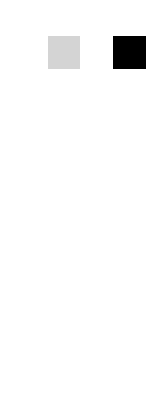
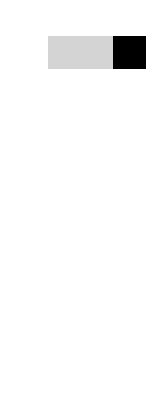
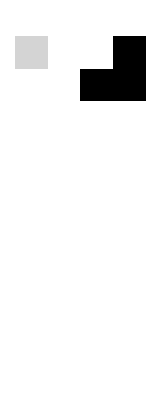
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
aa=aa+1;
A=IntegerDigits[aa];
Table[ArrayPlot[Table[Nest[t1,IntegerDigits[j,2],i],{i,1,10}]],{j,1,20}]
```

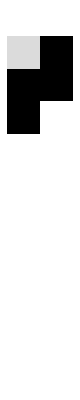
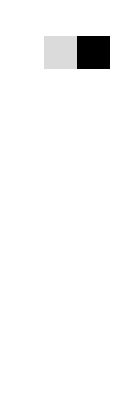
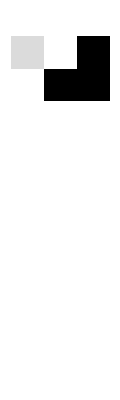
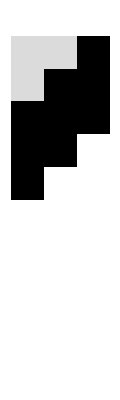
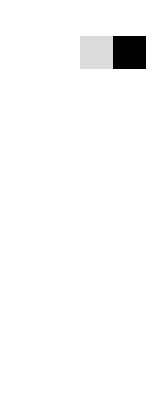
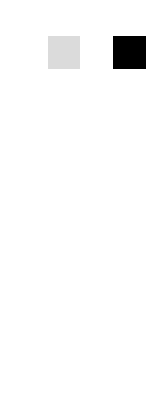
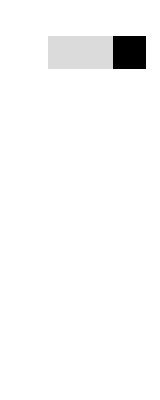
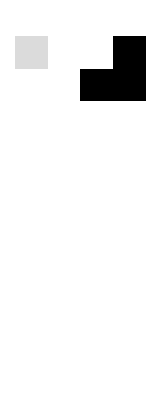
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
aa=aa+1;
A=IntegerDigits[aa];
Table[ArrayPlot[Table[Nest[t1,IntegerDigits[j,2],i],{i,1,10}]],{j,1,20}]
```

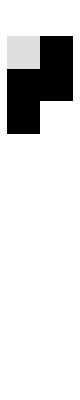
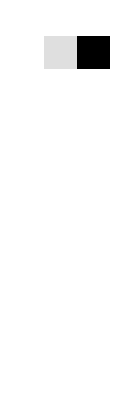
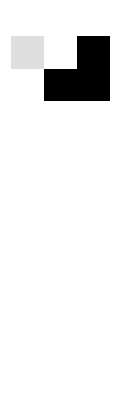
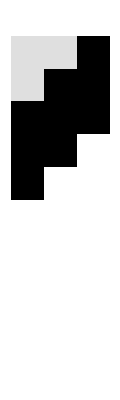
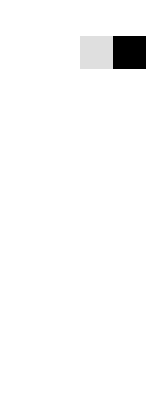
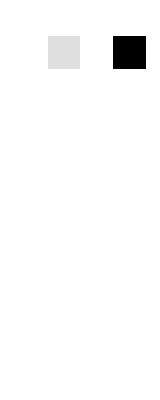
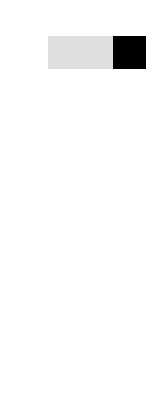
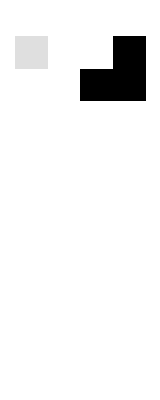
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
aa=aa+1;
A=IntegerDigits[aa];
Table[ArrayPlot[Table[Nest[t1,IntegerDigits[j,2],i],{i,1,10}]],{j,1,20}]
```

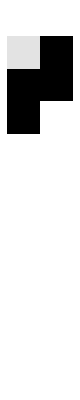
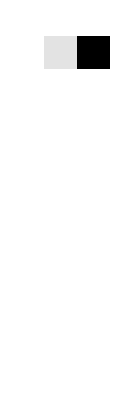
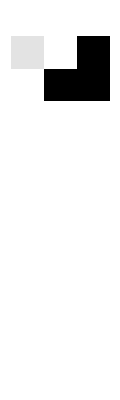
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
aa=aa+1;
A=IntegerDigits[aa];
Table[ArrayPlot[Table[Nest[t1,IntegerDigits[j,2],i],{i,1,10}]],{j,1,20}]
```

```mathematica
A=IntegerDigits[Prime[13]];
Table[ArrayPlot[Table[Nest[t1,IntegerDigits[j,2],i],{i,1,25}]],{j,1,250}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
2-tag system
Alphabet:{a,b,c,H}
Production rules:a-->ccbaH
b-->cca
c-->cc

Computation
Initial word:baa
acca
caccbaH
ccbaHcc
baHcccc
Hcccccca (halt).
```

```mathematica
tag2[x_,a_,b_,c_]:=Piecewise[{{x, First[x]==0}, {Delete[Join[a,x],{{1},{2}}], First[x]==1}, {Delete[Join[b,x],{{1},{2}}], First[x]==2}, {Delete[Join[c,x],{{1},{2}}], First[x]==3}}]
Map[ArrayPlot,Table[tag2[IntegerDigits[x,4],IntegerDigits[a,4],IntegerDigits[b,4],IntegerDigits[c,4]],{x,1,aa},{a,1,aa},{b,1,aa},{c,1,aa}],2]
```